# Good Graphics

## Andrew M. C. Dawes

Some tricks to generate descriptive plots (i.e. labels, nice size font etc.). It takes even more work to generate “publication quality” figures, but that is true for most computer algebra systems.

## Label the axes

As a Pacific Physics student, your ears should ring with the voices of your professors asking you what the units are for each axis.

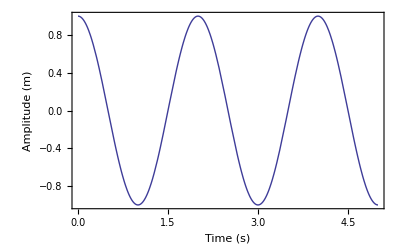

```mathematica
Plot[Re[Exp[I π t]],{t,0,5},Frame->True, FrameLabel->{"Time (s)","Amplitude (m)"},BaseStyle->{FontSize->16,FontWeight->Plain,FontFamily->"Myriad Pro"}]
```

## What is your uncertainty

If Dr. Brosing is at your talk you will get busted for leaving off the uncertainty. The tricky part with uncertainty, is that you have to have some to begin with... certainly.

### A plot without error bars (this is a no-no)

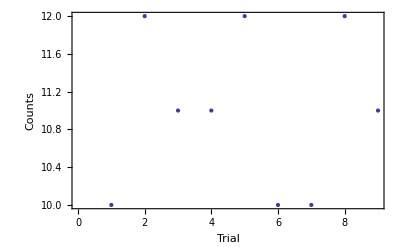

```mathematica
MadeUpData={10,12,11,11,12,10,10,12,11};
Uncert = MadeUpData * 0.10*Random[];
ListPlot[MadeUpData,Frame->True,FrameLabel->{"Trial","Counts"},BaseStyle->{FontSize->16,FontWeight->Plain,FontFamily->"Myriad Pro"}]
```

```mathematica
dataWithError = Partition[Riffle[MadeUpData,Uncert],2]
```

{{10,0.763531},{12,0.916238},{11,0.839885},{11,0.839885},{12,0.916238},{10,0.763531},{10,0.763531},{12,0.916238},{11,0.839885}}

### Load the ErrorBarPlots package (note the backtick before the endquote)

```mathematica
Needs["ErrorBarPlots`"]
```

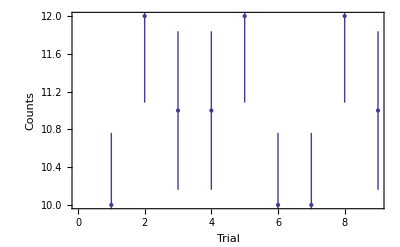

```mathematica
ErrorListPlot[dataWithError,Frame->True,FrameLabel->{"Trial","Counts"},BaseStyle->{FontSize->16,FontWeight->Plain,FontFamily->"Myriad Pro"}]
```

This is better but we still need to fiddle with the range to make the data fit. Here is how you do that:

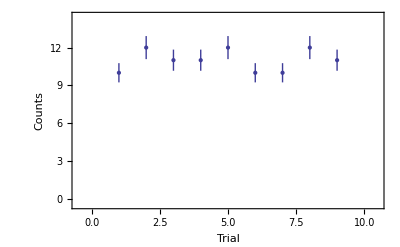

```mathematica
ErrorListPlot[dataWithError,Frame->True,FrameLabel->{"Trial","Counts"},BaseStyle->{FontSize->16,FontWeight->Plain,FontFamily->"Myriad Pro"},PlotRange->{{-0.5,10.5},{-0.5,14.5}}]
```

I was always taught to use a box frame plot with tick marks pointing inward. Also, set your axis range so that you have a nice number at the end and it is set in a bit from the extreme edge. Mathematica actually defaults to most of these options and you will find them to be fairly common among published physics papers.